```mathematica
SetOptions[EvaluationNotebook[],ShowCellLabel->False]
```

Calculations and notes in Quad 2.4, 25/05/2022 and references therein
Final figures with proper legend and colors etc in “../PhD_thesis/Chapter5/figs_create”

# Fold

Scaling k~Sqrt[p]

### Variance

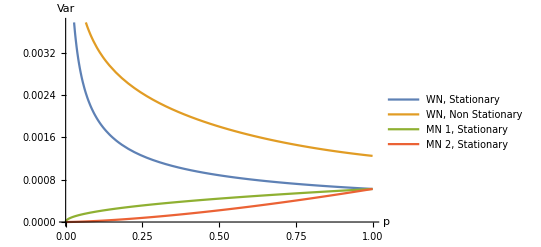

```mathematica
σ=0.05;
t={5};
k0=1;
a=1;
Plot[{(σ^2/(4*Sqrt[p])),((1-Sqrt[p])+Exp[-2*k0*(k0-Sqrt[p])+a*(k0-Sqrt[p])^2]*(1/(2*(k0-a*(k0-Sqrt[p])))))*0.05^2,σ^2*Sqrt[p]/4,σ^2*p^(3/2)/4},{p,0,1},AxesLabel->
{Style["p",18],Style["Var",18]},
PlotLegends->{"WN, Stationary","WN, Non Stationary","MN 1, Stationary","MN 2, Stationary"},PlotStyle->{Dashed[None],Dashed[None],Dashed[None]},LabelStyle->Directive[FontFamily->"Helvetica",FontSize->15]]
```

### Autocorrelation

A = Cov/Sqrt[Var]
For a stationary process, A = Exp[-Δ k τ]

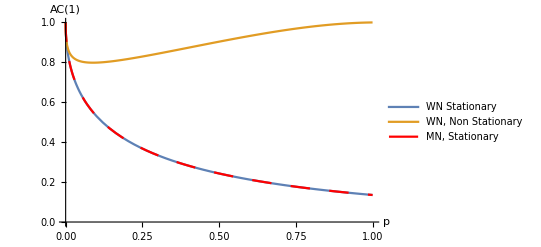

```mathematica
t1=3;
t2=5;
deltat=t2-t1;
k0=1.01;
Plot[{Exp[-2*Sqrt[p]],(Exp[-2*k0*(k0-Sqrt[p])+a*(k0-Sqrt[p])^2]/(2*(k0-a*(k0-Sqrt[p])))+(ⅇ^((-2 k0+a (k0-Sqrt[p]))^2/(2 a)) √(π/2) (Erf[(√2 k0)/(√a)]+Erf[(-2 k0+a (k0-Sqrt[p]))/(√2 √a)]))/(√a))/((k0-Sqrt[p])+Exp[-2*k0*(k0-Sqrt[p])+a*(k0-Sqrt[p])^2]*(1/(2*(k0-a*(k0-Sqrt[p]))))),Exp[-2*Sqrt[p]]},{p,0,1},PlotLegends->{"WN Stationary","WN, Non Stationary","MN, Stationary"},AxesLabel->{Style["p",18],Style["AC(1)",18]},PlotStyle->{Dashed[None],Dashed[None],{Dashing[Large],Red}},LabelStyle->Directive[FontFamily->"Helvetica",FontSize->15]]
```

### Coefficient Variation

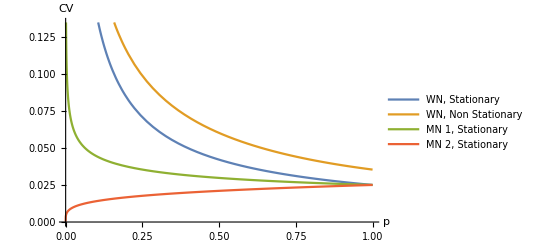

```mathematica
Plot[{σ/(2*p^(3/4)),Sqrt[((1-Sqrt[p])+Exp[-2*k0*(k0-Sqrt[p])+a*(k0-Sqrt[p])^2]*(1/(2*(k0-a*(k0-Sqrt[p])))))*0.05^2]/(Sqrt[p]),Sqrt[σ^2/4]/(p^(1/4)),Sqrt[σ^2/4]*(p^(1/4))},{p,0,1},AxesLabel->{Style["p",18],Style["CV",18]},PlotLegends->{"WN, Stationary","WN, Non Stationary","MN 1, Stationary","MN 2, Stationary"},LabelStyle->Directive[FontFamily->"Helvetica",FontSize->15]]
```

### Measurement uncertainties

#### On Variance

Let us imagine we have measurement errors that account for a second σ_2 in addition to the O-U σ. Then the variance is shifted by a term Var+σ_2. Plot below shows the effect of different intrinsic noise levels on the variance ([[1]],[[2]],[[3]]) and of measurement uncertainties [[4]]. As we can see, the measurement uncertainties are less impactful on the leading indicator than the intrinsic noise, especially when approaching the bifurcation.

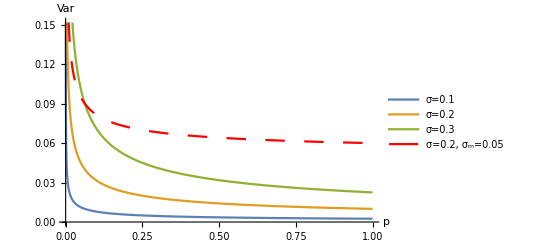

```mathematica
d3={0.1,0.2,0.3};
Plot[{(d3[[1]]^2/(4*Sqrt[p])),(d3[[2]]^2/(4*Sqrt[p])),(d3[[3]]^2/(4*Sqrt[p])),((d3[[2]]^2/(4*Sqrt[p]))+0.05)},{p,0,1},AxesLabel->
{Style["p",18],Style["Var",18]},PlotStyle->{Dashed[None],Dashed[None],Dashed[None],{Dashing[Large],Red}},LabelStyle->Directive[FontFamily->"Helvetica",FontSize->15],PlotLegends->Placed[LineLegend[{"σ=0.1","σ=0.2","σ=0.3","σ=0.2, σ_m=0.05"},LabelStyle->{GrayLevel[0.2],16},LegendLayout->{"Row",2}],{0.55,0.75}]]
```

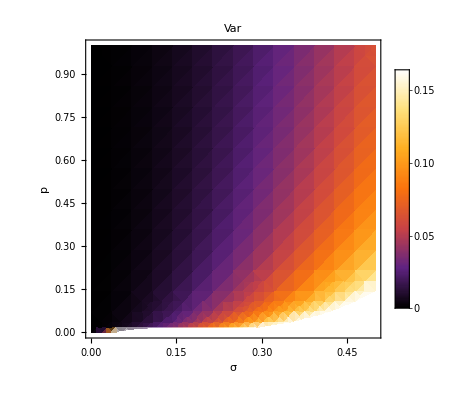

```mathematica
DensityPlot[(sigma^2/(4*Sqrt[p])),{sigma,0,0.5},{p,0,1},ColorFunction->ColorData["SunsetColors"],PlotLegends->Automatic,FrameLabel->{Style["σ",20],Style["p",20]},PlotLabel->Style["Var",FontSize->20],FrameTicksStyle->Directive[Black,18]] (* Original *)
```

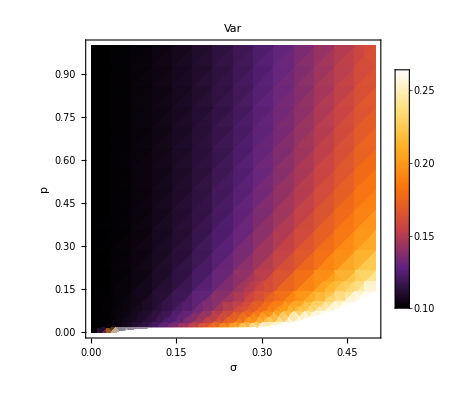

```mathematica
newsigma = 0.1;
DensityPlot[(sigma^2/(4*Sqrt[p])+newsigma),{sigma,0,0.5},{p,0,1},ColorFunction->ColorData["SunsetColors"],PlotLegends->Automatic,FrameLabel->{Style["σ",20],Style["p",20]},PlotLabel->Style["Var",FontSize->20],FrameTicksStyle->Directive[Black,18]] (* With measurement error *)
```

#### On autocorrelation

As for the variance, let us imagine to add some additive uncertainty coming from measurement imperfections. The autocorrelation is impacted by a larger variance that normalize it. See analytical derivation on Quad 2.1, 21/11/19.

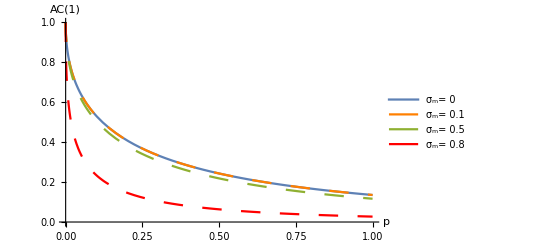

```mathematica
d1=0.5;
sigmaMeas = {0,0.1,0.5,0.8}; (* measurement uncertainty variance *)
Plot[{Exp[-2*Sqrt[p]],
(Exp[-2*Sqrt[p]]*d1^2)/(4*Sqrt[p]*(sigmaMeas[[1]]^2+d1^2/(4*Sqrt[p]))),
(Exp[-2*Sqrt[p]]*d1^2)/(4*Sqrt[p]*(sigmaMeas[[2]]^2+d1^2/(4*Sqrt[p]))),
(Exp[-2*Sqrt[p]]*d1^2)/(4*Sqrt[p]*(sigmaMeas[[3]]^2+d1^2/(4*Sqrt[p])))},{p,0,1},AxesLabel->{Style["p",18],Style["AC(1)",18]},PlotStyle->{Dashed[None],{Dashing[Large],Orange},{Dashing[Large]},{Dashing[Large],Red}},PlotLegends->Placed[LineLegend[{"σ_m= 0","σ_m= 0.1","σ_m= 0.5","σ_m= 0.8"},LabelStyle->{GrayLevel[0.2],16},LegendLayout->{"Row",2}],{0.55,0.75}],LabelStyle->Directive[FontFamily->"Helvetica",FontSize->15]]
```

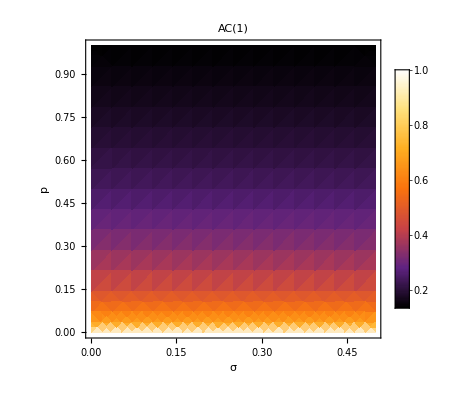

```mathematica
DensityPlot[Exp[-2*Sqrt[p]],{sigma,0,0.5},{p,0,1},ColorFunction->ColorData["SunsetColors"],PlotLegends->Automatic,FrameLabel->{Style["σ",20],Style["p",20]},PlotLabel->Style["AC(1)",FontSize->20],FrameTicksStyle->Directive[Black,18]]
```

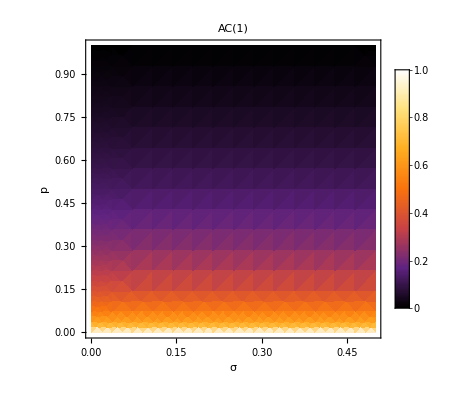

```mathematica
DensityPlot[(Exp[-2*Sqrt[p]]*sigma^2)/(4*Sqrt[p]*(sigmaMeas[[1]]^2+sigma^2/(4*Sqrt[p]))),{sigma,0,0.5},{p,0,1},ColorFunction->ColorData["SunsetColors"],FrameLabel->{Style["σ",20],Style["p",20]},PlotLabel->Style["AC(1)",FontSize->20],FrameTicksStyle->Directive[Black,18],PlotLegends->Placed[BarLegend[{Automatic,{0,1}}],Right]]
```

#### “Realistic” fold

CV where x_mean is capped by some value and does not go until 0 (Quad 2.4, 25/5/22)

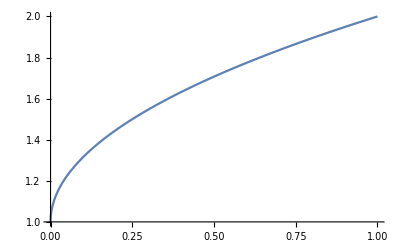

```mathematica
Plot[1+Sqrt[p],{p,0,1}] (* this is the mean *)
```

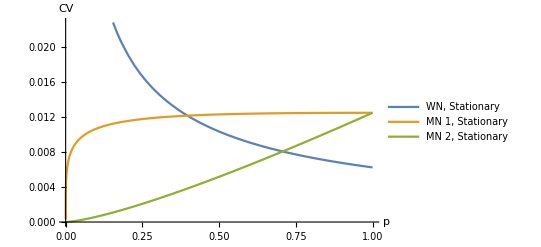

```mathematica
Plot[{σ/(4*p^(1/2))*1/(1+Sqrt[p]),Sqrt[σ^2/4]*p^(1/4)/(1+Sqrt[p]),Sqrt[σ^2/4]*(p^(3/2))/(1+Sqrt[p])},{p,0,1},AxesLabel->{Style["p",18],Style["CV",18]},PlotLegends->{"WN, Stationary","MN 1, Stationary","MN 2, Stationary"},LabelStyle->Directive[FontFamily->"Helvetica",FontSize->15]]
```

# Transcritical

### Variance

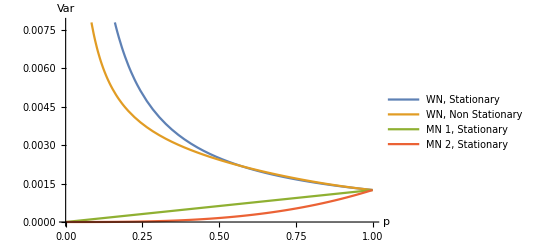

```mathematica
σ=0.05;
σmeas=0.005;
t={5};
Plot[{(σ^2/(2*p)),((1-p)+Exp[-2*k0*(k0-p)+a*(k0-p)^2]*(1/(2*(k0-a*(k0-p)))))*0.05^2,σ^2*p/2,0.5*σ^2*p^3},{p,0,1},AxesLabel->
{Style["p",18],Style["Var",18]},PlotLegends->{"WN, Stationary","WN, Non Stationary","MN 1, Stationary","MN 2, Stationary"},PlotStyle->{Dashed[None],Dashed[None],Dashed[None]},LabelStyle->Directive[FontFamily->"Helvetica",FontSize->15]] (*MN 1 corresponds to h = sigma x, MN 2 to h = sigma x^2 *)
```

### Autocorrelation

A = Cov/Sqrt[Var]
For a stationary process, A = Exp[-Δ k τ]

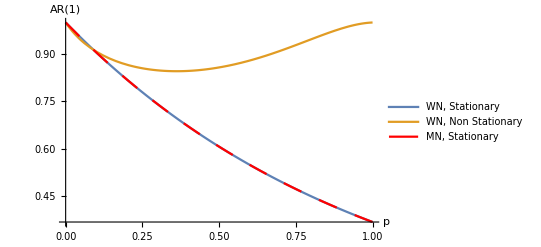

```mathematica
t1=3;
t2=5;
deltat=t2-t1;
k0=1.01;
Plot[{Exp[-p],(Exp[-2*k0*(k0-p)+a*(k0-p)^2]/(2*(k0-a*(k0-p)))+(ⅇ^((k0-a (k0-p))^2/a) √π (Erf[k0/(√a)]+Erf[(-k0+a (k0-p))/(√a)]))/(2 √a))/((k0-p)+Exp[-2*k0*(k0-p)+a*(k0-p)^2]*(1/(2*(k0-a*(k0-p))))),Exp[-p]},{p,0,1},PlotLegends->{"WN, Stationary","WN, Non Stationary","MN, Stationary"},AxesLabel->{Style["p",18],Style["AR(1)",18]},PlotStyle->{Dashed[None],Dashed[None],{Dashing[Large],Red}},LabelStyle->Directive[FontFamily->"Helvetica",FontSize->15]]
```

### Coefficient Variation

doublecheck x_0 > p

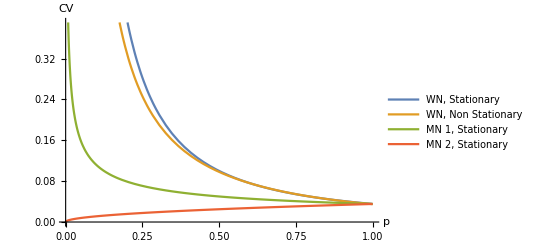

```mathematica
Plot[{σ/(Sqrt[2]*p^(3/2)),Sqrt[((1-p)+Exp[-2*k0*(k0-p)+a*(k0-p)^2]*(1/(2*(k0-a*(k0-p)))))*0.05^2]/(p),Sqrt[σ^2/(2*p)],Sqrt[p*σ^2/(2)]},{p,0,1},AxesLabel->{Style["p",18],Style["CV",18]},PlotLegends->{"WN, Stationary","WN, Non Stationary","MN 1, Stationary","MN 2, Stationary"},LabelStyle->Directive[FontFamily->"Helvetica",FontSize->15]]
```

# Pitchfork

They are the same for subcritical and supercritical (used as a non-critical example)

### Variance

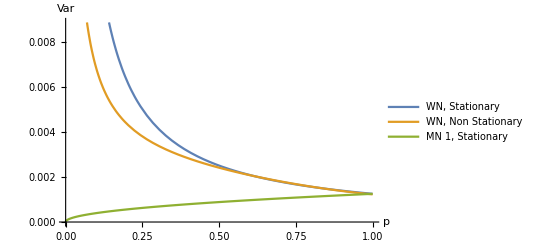

```mathematica
σ=0.05;
t={5};
Plot[{(σ^2/(2*p)),((1-p)+Exp[-2*k0*(k0-p)+a*(k0-p)^2]*(1/(2*(k0-a*(k0-p)))))*0.05^2,σ^2*Sqrt[p]/2},{p,0,1},AxesLabel->
{Style["p",18],Style["Var",18]},PlotLegends->{"WN, Stationary","WN, Non Stationary","MN 1, Stationary"},PlotStyle->{Dashed[None],Dashed[None],Dashed[None]},LabelStyle->Directive[FontFamily->"Helvetica",FontSize->15]]
```

### Autocorrelation

A = Cov/Sqrt[Var]
For a stationary process, A = Exp[-Δ k τ]

```mathematica
t1=3;
t2=5;
deltat=t2-t1;
k0=1.01;
Plot[{Exp[-p],(Exp[-2*k0*(k0-p)+a*(k0-p)^2]/(2*(k0-a*(k0-p)))+(ⅇ^((k0-a (k0-p))^2/a) √π (Erf[k0/(√a)]+Erf[(-k0+a (k0-p))/(√a)]))/(2 √a))/((k0-p)+Exp[-2*k0*(k0-p)+a*(k0-p)^2]*(1/(2*(k0-a*(k0-p))))),Exp[-p]},{p,0,1},PlotLegends->{"WN, Stationary","WN, Non Stationary","MN, Stationary"},AxesLabel->{Style["p",18],Style["AR(1)",18]},PlotStyle->{Dashed[None],Dashed[None],{Dashing[Large],Red}},LabelStyle->Directive[FontFamily->"Helvetica",FontSize->15]]
```

-Graphics-

### Coefficient Variation

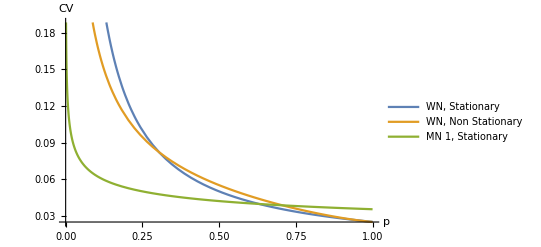

```mathematica
Plot[{σ/(2*p),Sqrt[((1-p)+Exp[-4*k0*(1-p)+a*2*(1-p)^2]/(4*(k0-a*(1-p))))*0.05^2]/Sqrt[p],Sqrt[σ^2/2]/p^(1/4)},{p,0,1},AxesLabel->{Style["p",18],Style["CV",18]},PlotLegends->{"WN, Stationary","WN, Non Stationary","MN 1, Stationary"},LabelStyle->Directive[FontFamily->"Helvetica",FontSize->15]]
(* CV for x0 ≥ p: ,Sqrt[σ^2/2]*p^(1/4)/(1-p) *)
```